```mathematica
(* SIR (Cowpox) PREVALENCE *)
```

```mathematica
(* Turn off Solve warning messages *)
Off[Solve::ratnz]

(* Function to generate table of mean burdens for ρ=0 and ρ=1, for all θ1 and θ2 combinations *)
provchange[pars_]:=
Module[{data},
data= Table[Table[Solve[system//.provpars//.pars,{p,n}][[1]],{prov,0,1}],{θ1,0,5},{θ2,0,5}];
Table[(p/.data[[i]][[j]][[2]])-(p/.data[[i]][[j]][[1]]),{i,1,6},{j,1,6}]
]

(* Provisioning response calculations *)
provpars={δp->δmin+(δmax-δmin)*E^(-θ1*prov),αp->αmax-(αmax-αmin)*E^(-θ2*prov)};

(* System equations *)
system={(1-p)*αp*δp*p*n-γ*p-p*b*(K-n)/K==0 && b*n*(K-n)/K-μ*n==0};
```

```mathematica
(* GENERATE PLOTS VARYING BY K *)

(* Compile parameter lists *)
pars1={K->42.12,b->1.24,γ->1/4,ν->0,δmin->δmax/2,δmax->0.089,αmin->1*^-1,αmax->2*^-1,μ ->1/13.75};
pars2={K->42.12*1.5,b->1.24,γ->1/4,ν->0,δmin->δmax/2,δmax->0.089,αmin->1*^-1,αmax->2*^-1,μ ->1/13.75};
pars3={K->42.12*2,b->1.24,γ->1/4,ν->0,δmin->δmax/2,δmax->0.089,αmin->1*^-1,αmax->2*^-1,μ ->1/13.75};

(* Generate tables of differences in predicted prevalences for all θ1 and θ2 combinations *)
resprevh1 =provchange[pars1]
resprevh2 =provchange[pars2]
resprevh3 =provchange[pars3]
```

{{0.,0.354205,0.424086,0.4456,0.453048,0.455728},{-0.422628,0.0952603,0.197435,0.228891,0.239781,0.2437},{-0.696515,-0.0725497,0.0505523,0.0884524,0.101572,0.106294},{-0.827802,-0.152989,-0.0198557,0.021133,0.0353215,0.0404284},{-0.88165,-0.185982,-0.0487338,-0.00647835,0.00814861,0.0134134},{-0.902306,-0.198638,-0.0598117,-0.0170703,-0.00227517,0.00305012}}

{{0.,0.236136,0.282724,0.297067,0.302032,0.303819},{-0.281752,0.0635069,0.131623,0.152594,0.159854,0.162467},{-0.464343,-0.0483665,0.0337015,0.0589683,0.0677145,0.0708626},{-0.551868,-0.101993,-0.0132371,0.0140887,0.0235476,0.0269522},{-0.587767,-0.123988,-0.0324892,-0.0043189,0.00543241,0.00894224},{-0.601538,-0.132426,-0.0398745,-0.0113802,-0.00151678,0.00203341}}

{{0.,0.177102,0.212043,0.2228,0.226524,0.227864},{-0.211314,0.0476302,0.0987173,0.114446,0.11989,0.12185},{-0.348257,-0.0362749,0.0252761,0.0442262,0.0507859,0.0531469},{-0.413901,-0.0764947,-0.00992783,0.0105665,0.0176607,0.0202142},{-0.440825,-0.092991,-0.0243669,-0.00323918,0.00407431,0.00670668},{-0.451153,-0.0993191,-0.0299059,-0.00853517,-0.00113758,0.00152506}}

-1.

0.5

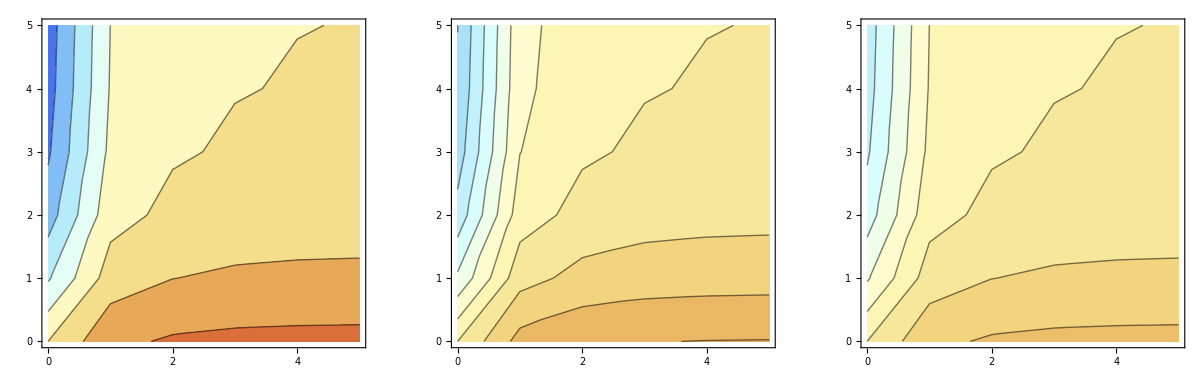

```mathematica
(* Calculate min and max values across all resprevh arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[resprevh1,resprevh2,resprevh3]*10]/10//N
maxvals=Ceiling[Max[resprevh1,resprevh2,resprevh3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[resprevh1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[resprevh2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[resprevh3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```

```mathematica
(* GENERATE PLOTS VARYING BY b *)

(* Compile parameter lists *)
pars1={K->42.12,b->1.24,γ->1/4,ν->0,δmin->δmax/2,δmax->0.089,αmin->1*^-1,αmax->2*^-1,μ ->1/13.75};
pars2={K->42.12,b->1.24*1.5,γ->1/4,ν->0,δmin->δmax/2,δmax->0.089,αmin->1*^-1,αmax->2*^-1,μ ->1/13.75};
pars3={K->42.12,b->1.24*2,γ->1/4,ν->0,δmin->δmax/2,δmax->0.089,αmin->1*^-1,αmax->2*^-1,μ ->1/13.75};

(* Generate tables of differences in predicted prevalences for all θ1 and θ2 combinations *)
resprevh1 =provchange[pars1]
resprevh2 =provchange[pars2]
resprevh3 =provchange[pars3]
```

{{0.,0.354205,0.424086,0.4456,0.453048,0.455728},{-0.422628,0.0952603,0.197435,0.228891,0.239781,0.2437},{-0.696515,-0.0725497,0.0505523,0.0884524,0.101572,0.106294},{-0.827802,-0.152989,-0.0198557,0.021133,0.0353215,0.0404284},{-0.88165,-0.185982,-0.0487338,-0.00647835,0.00814861,0.0134134},{-0.902306,-0.198638,-0.0598117,-0.0170703,-0.00227517,0.00305012}}

{{0.,0.346998,0.415457,0.436534,0.44383,0.446456},{-0.41403,0.0933222,0.193418,0.224234,0.234902,0.238742},{-0.682343,-0.0710736,0.0495237,0.0866527,0.0995052,0.104131},{-0.810959,-0.149877,-0.0194517,0.020703,0.0346028,0.0396058},{-0.863712,-0.182198,-0.0477422,-0.00634654,0.00798282,0.0131405},{-0.883948,-0.194597,-0.0585948,-0.016723,-0.00222888,0.00298806}}

{{0.,0.343504,0.411273,0.432138,0.439361,0.44196},{-0.40986,0.0923824,0.19147,0.221976,0.232536,0.236337},{-0.675472,-0.0703579,0.049025,0.0857801,0.0985031,0.103083},{-0.802793,-0.148367,-0.0192558,0.0204945,0.0342543,0.039207},{-0.855014,-0.180363,-0.0472614,-0.00628263,0.00790243,0.0130081},{-0.875046,-0.192637,-0.0580047,-0.0165546,-0.00220643,0.00295797}}

-1.

0.5

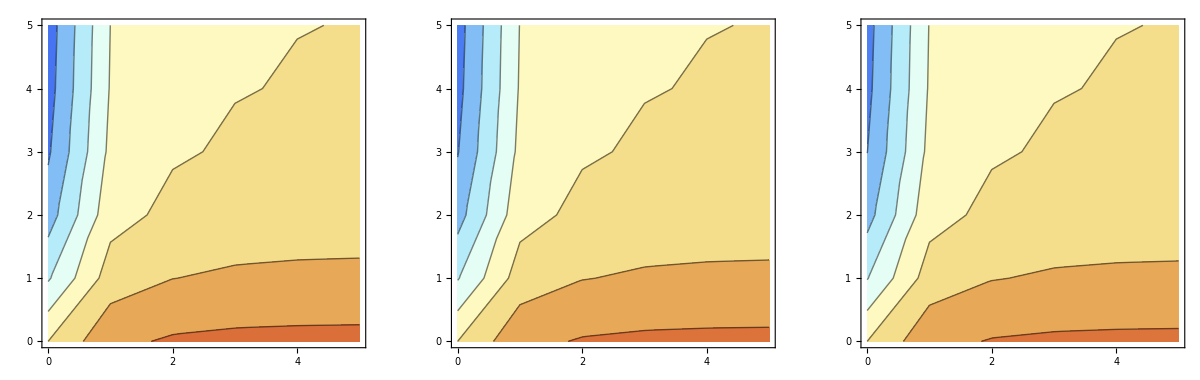

```mathematica
(* Calculate min and max values across all resprevh arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[resprevh1,resprevh2,resprevh3]*10]/10//N
maxvals=Ceiling[Max[resprevh1,resprevh2,resprevh3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[resprevh1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[resprevh2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[resprevh3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```

```mathematica
(* GENERATE PLOTS VARYING BY μ *)

(* Compile parameter lists *)
pars1={K->42.12,b->1.24,γ->1/4,ν->0,δmin->δmax/2,δmax->0.089,αmin->1*^-1,αmax->2*^-1,μ ->1/13.75};
pars2={K->42.12,b->1.24,γ->1/4,ν->0,δmin->δmax/2,δmax->0.089,αmin->1*^-1,αmax->2*^-1,μ ->1/13.75/1.5};
pars3={K->42.12,b->1.24,γ->1/4,ν->0,δmin->δmax/2,δmax->0.089,αmin->1*^-1,αmax->2*^-1,μ ->1/13.75/2};

(* Generate tables of differences in predicted prevalences for all θ1 and θ2 combinations *)
resprevh1 =provchange[pars1]
resprevh2 =provchange[pars2]
resprevh3 =provchange[pars3]
```

{{0.,0.354205,0.424086,0.4456,0.453048,0.455728},{-0.422628,0.0952603,0.197435,0.228891,0.239781,0.2437},{-0.696515,-0.0725497,0.0505523,0.0884524,0.101572,0.106294},{-0.827802,-0.152989,-0.0198557,0.021133,0.0353215,0.0404284},{-0.88165,-0.185982,-0.0487338,-0.00647835,0.00814861,0.0134134},{-0.902306,-0.198638,-0.0598117,-0.0170703,-0.00227517,0.00305012}}

{{0.,0.320933,0.384249,0.403743,0.410491,0.41292},{-0.382929,0.086312,0.178889,0.207391,0.217257,0.220808},{-0.631088,-0.0657348,0.0458036,0.0801436,0.0920306,0.0963091},{-0.750042,-0.138618,-0.0179905,0.0191479,0.0320035,0.0366307},{-0.798832,-0.168512,-0.044156,-0.00586981,0.00738317,0.0121534},{-0.817548,-0.179979,-0.0541933,-0.0154668,-0.00206145,0.00276361}}

{{0.,0.304799,0.364933,0.383447,0.389855,0.392162},{-0.363679,0.0819731,0.169896,0.196965,0.206335,0.209708},{-0.599362,-0.0624302,0.0435011,0.0761147,0.0874042,0.0914676},{-0.712337,-0.13165,-0.0170861,0.0181853,0.0303947,0.0347893},{-0.758674,-0.160041,-0.0419362,-0.00557473,0.00701202,0.0115424},{-0.77645,-0.170932,-0.051469,-0.0146893,-0.00195782,0.00262468}}

-1.

0.5

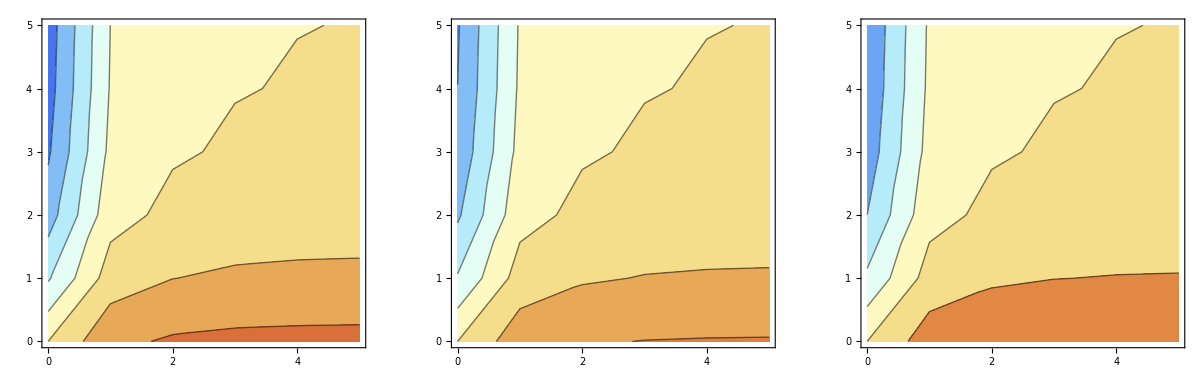

```mathematica
(* Calculate min and max values across all resprevh arrays, rounding up/down to nearest value to 1 decimal place *)
(* Note, these scale within the above 3 generated plots; to scale across all parasites would need to calculate min and maxvals across them all *)
minvals=Floor[Min[resprevh1,resprevh2,resprevh3]*10]/10//N
maxvals=Ceiling[Max[resprevh1,resprevh2,resprevh3]*10]/10//N

(* Now create all 3 graphs, using the same common min and max values *)
p1=ListContourPlot[resprevh1,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p2=ListContourPlot[resprevh2,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
p3=ListContourPlot[resprevh3,PlotLegends->None,ColorFunctionScaling->False,ColorFunction->ColorData[{"LightTemperatureMap",{minvals,maxvals}}],FrameTicks->{{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None},{{{1,0},{2,1},{3,2},{4,3},{5,4},{6,5}},None}}];
Show[GraphicsGrid[{{p1,p2,p3}}]]

(* Create a legend spanning specified range (minvals to maxvals) *)
BarLegend[{"LightTemperatureMap",{minvals,maxvals}}]
```